```mathematica
(* Import data from Johns Hopkins *)
HopkinsConfirmed = Drop[Import["~/Documents/Wolfram Mathematica/covid19be/johns-hopkins-data/time_series_covid19_confirmed_global.csv",CharacterEncoding->"UTF8"],1];
HopkinsRecovered = Drop[Import["~/Documents/Wolfram Mathematica/covid19be/johns-hopkins-data/time_series_covid19_recovered_global.csv",CharacterEncoding->"UTF8"],1];
HopkinsDeaths = Drop[Import["~/Documents/Wolfram Mathematica/covid19be/johns-hopkins-data/time_series_covid19_deaths_global.csv",CharacterEncoding->"UTF8"],1];
CountryList=AlphabeticSort[DeleteDuplicates[Transpose[HopkinsConfirmed][[2]]]];
```

```mathematica
(* Data for countries can be split over multiple rows in the data from Hopkins *)
DataByCountry = Table[{},{i,1,Length[CountryList]}];
NumberOfDays = Length[Transpose[HopkinsConfirmed]]-4;

For[country = 1, country ≤ Length[CountryList],country++,
TempConfirmed=Table[0,{i,1,NumberOfDays}];
TempRecovered = Table[0,{i,1,NumberOfDays}];
TempDeaths = Table[0,{i,1,NumberOfDays}];
For[row=1,row≤ Length[HopkinsConfirmed],row++,
If[StringMatchQ[CountryList[[country]], HopkinsConfirmed[[row,2]]],
(* Country name of ConfirmedByCountry matches current row *)
TempConfirmed = TempConfirmed + Drop[HopkinsConfirmed[[row]],4];
]
];

For[row=1,row≤ Length[HopkinsRecovered],row++,
If[StringMatchQ[CountryList[[country]], HopkinsRecovered[[row,2]]],
(* Country name of ConfirmedByCountry matches current row *)
TempRecovered= TempRecovered + Drop[HopkinsRecovered[[row]],4];
]
];

For[row=1,row≤ Length[HopkinsDeaths],row++,
If[StringMatchQ[CountryList[[country]], HopkinsDeaths[[row,2]]],
(* Country name of ConfirmedByCountry matches current row *)
TempDeaths = TempDeaths + Drop[HopkinsDeaths[[row]],4];
]
];
TempConfirmedDiff=TempConfirmed-Drop[Join[{0},TempConfirmed],-1];
TempRecoveredDiff=TempRecovered-Drop[Join[{0},TempRecovered],-1];
TempDeathsDiff=TempDeaths-Drop[Join[{0},TempDeaths],-1];
DataByCountry[[country]]= {ToString[CountryList[[country]]],TempConfirmed,TempRecovered,TempDeaths,TempConfirmedDiff,TempRecoveredDiff,TempDeathsDiff};
]
```

```mathematica
(* Model *)
SIR[country_,dday_] := (
n=n0;
i=i0;
r=0;
m=0;
c=r+r+m;
s = n-i-r-m;
cost = 0;
For[sirday=1,sirday≤ dday, sirday++,
lambda = gamma * listr0[[sirday]][[2]];
ds = -lambda i *(s/n);
di = lambda i * (s/n) -gamma i - delta i;
dr = gamma i;
dm = delta i;
dc=di +dr+dm;
s+=ds;
i+=di;
r+=dr;
m+=dm;
c+=dc;
n=s+i+r;
If[sirday≤ Length[DataByCountry[[country]][[2]]],
cost = cost + (c-DataByCountry[[country]][[2]][[sirday]])^2;];
];
Return[{s,i,r,m,c,cost,di}];
);
```

```mathematica
(* Initial values for this country *)
Window =2;
CurrentCountry = 163;

vandaag = Length[DataByCountry[[CurrentCountry]][[2]]];
CFR=DataByCountry[[CurrentCountry]][[4]][[-1]]/DataByCountry[[CurrentCountry]][[2]][[-1]];

n0 = 11400000;
i0=100;
gamma=(1-CFR)/12;
delta = CFR/28;
listr0 = {};
For[day = 1, day <= Length[DataByCountry[[CurrentCountry]][[2]]] + 60, day++,
  listr0 = Join[listr0, {{day, 4.3}}];
  ];
```

```mathematica
(* Fit model to the data *)
For[day=1,day≤Length[DataByCountry[[CurrentCountry]][[2]]]-Window,day++,
bestr0=listr0[[day]][[2]];
bestcost=SIR[CurrentCountry,day+Window][[6]];
For[kr0 = 0.01,kr0≤7,kr0=kr0+0.02,
(* set this possible r0 for all folliwing days and see what the cost is *)
For[j = 0, j <= Length[listr0] - day, j++,
listr0[[day + j]][[2]] = kr0;];
temp=SIR[CurrentCountry,day + Window];
If[temp[[6]]<bestcost,bestcost=temp[[6]];bestr0=kr0;];
];

(* We found a good r0 for this day, set it for all the following days *)
For[j = 0, j <= Length[listr0] - day, j++,
listr0[[day + j]][[2]] =bestr0;];
];

(* Generate the lists of data for the plots *)
lists={};
listi={};
listr={};
listm={};
listc={};
listdi={};
For[day=1,day≤Length[DataByCountry[[CurrentCountry]][[2]]]+60,day++,
temp=SIR[CurrentCountry,day];
lists=Append[lists,{day,temp[[1]]}];
listi=Append[listi,{day,temp[[2]]}];
listr=Append[listr,{day,temp[[3]]}];
listm=Append[listm,{day,temp[[4]]}];
listc=Append[listc,{day,temp[[5]]}];
listdi=Append[listdi,{day,temp[[7]]}];
];
```

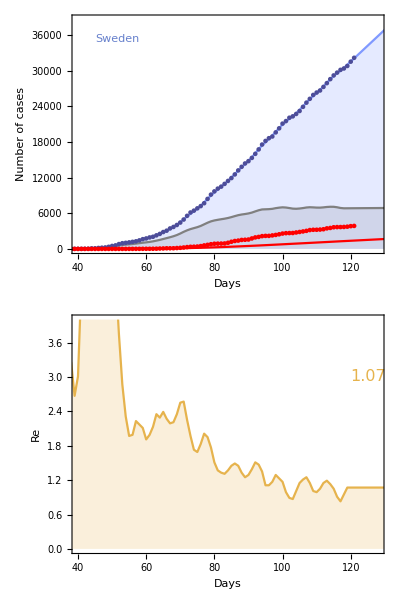

```mathematica
(* Generate plots *)
If[listr0[[-1]][[2]]<0.8,R0Color=RGBColor[0.3,0.7,0.3],If[listr0[[-1]][[2]]>1.2,R0Color=RGBColor[0.7,0.3,0.3],R0Color=RGBColor[0.9,0.7,0.3]]];
plotFinalR0 = Graphics[{Text[Style[listr0[[-1]][[2]], FontSize->16,R0Color],{120,3},{Left,Center}]}];

plotCountryname = Graphics[{Text[Style[DataByCountry[[CurrentCountry]][[1]], Large,RGBColor[0.4,0.5,0.8]],{45,1.1 Max[DataByCountry[[CurrentCountry]][[2]]]},{Left,Center}]}];

plotModel=Show[{ListPlot[{listi,listc,listm,DataByCountry[[CurrentCountry]][[2]],DataByCountry[[CurrentCountry]][[4]]},PlotRange->{{40,vandaag+7},{0,1.2 Max[DataByCountry[[CurrentCountry]][[2]]]}},Joined->{True,True,True,False,False},Filling->{1-> Bottom,2->Bottom},PlotStyle->{Gray,RGBColor[0.5,0.6,1],Red,RGBColor[0.3,0.3,0.6],Red},FrameLabel->{"Days","Number of cases"},Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Thickness[0.002],13],AspectRatio->1/1,ImageSize->600],plotCountryname}];

plotR0=ListPlot[listr0,Joined->True,Filling->{1->Bottom},PlotStyle->R0Color,FrameLabel->{"Days","Re"},FrameStyle->Directive[Thickness[0.002],13],Frame->True,FrameTicks->Automatic,AspectRatio->1/8,PlotRange->{{40,vandaag+7},{0,4}},ImageSize->600];

ThePlotThickens=Multicolumn[{Show[plotModel,ImagePadding->{{70,10},{20,10}}],Show[{plotR0,plotFinalR0},ImagePadding->{{70,10},{40,5}}]},1]

Export["Desktop/SIR-belgium-22may.pdf", ThePlotThickens, ImageResolution -> 600];
```

```mathematica
TableForm[Table[{i,CountryList[[i]]},{i,1,Length[CountryList]}]]
```

1 | Afghanistan
2 | Albania
3 | Algeria
4 | Andorra
5 | Angola
6 | Antigua and Barbuda
7 | Argentina
8 | Armenia
9 | Australia
10 | Austria
11 | Azerbaijan
12 | Bahamas
13 | Bahrain
14 | Bangladesh
15 | Barbados
16 | Belarus
17 | Belgium
18 | Belize
19 | Benin
20 | Bhutan
21 | Bolivia
22 | Bosnia and Herzegovina
23 | Botswana
24 | Brazil
25 | Brunei
26 | Bulgaria
27 | Burkina Faso
28 | Burma
29 | Burundi
30 | Cabo Verde
31 | Cambodia
32 | Cameroon
33 | Canada
34 | Central African Republic
35 | Chad
36 | Chile
37 | China
38 | Colombia
39 | Comoros
40 | Congo (Brazzaville)
41 | Congo (Kinshasa)
42 | Costa Rica
43 | Cote d'Ivoire
44 | Croatia
45 | Cuba
46 | Cyprus
47 | Czechia
48 | Denmark
49 | Diamond Princess
50 | Djibouti
51 | Dominica
52 | Dominican Republic
53 | Ecuador
54 | Egypt
55 | El Salvador
56 | Equatorial Guinea
57 | Eritrea
58 | Estonia
59 | Eswatini
60 | Ethiopia
61 | Fiji
62 | Finland
63 | France
64 | Gabon
65 | Gambia
66 | Georgia
67 | Germany
68 | Ghana
69 | Greece
70 | Grenada
71 | Guatemala
72 | Guinea
73 | Guinea-Bissau
74 | Guyana
75 | Haiti
76 | Holy See
77 | Honduras
78 | Hungary
79 | Iceland
80 | India
81 | Indonesia
82 | Iran
83 | Iraq
84 | Ireland
85 | Israel
86 | Italy
87 | Jamaica
88 | Japan
89 | Jordan
90 | Kazakhstan
91 | Kenya
92 | Korea, South
93 | Kosovo
94 | Kuwait
95 | Kyrgyzstan
96 | Laos
97 | Latvia
98 | Lebanon
99 | Lesotho
100 | Liberia
101 | Libya
102 | Liechtenstein
103 | Lithuania
104 | Luxembourg
105 | Madagascar
106 | Malawi
107 | Malaysia
108 | Maldives
109 | Mali
110 | Malta
111 | Mauritania
112 | Mauritius
113 | Mexico
114 | Moldova
115 | Monaco
116 | Mongolia
117 | Montenegro
118 | Morocco
119 | Mozambique
120 | MS Zaandam
121 | Namibia
122 | Nepal
123 | Netherlands
124 | New Zealand
125 | Nicaragua
126 | Niger
127 | Nigeria
128 | North Macedonia
129 | Norway
130 | Oman
131 | Pakistan
132 | Panama
133 | Papua New Guinea
134 | Paraguay
135 | Peru
136 | Philippines
137 | Poland
138 | Portugal
139 | Qatar
140 | Romania
141 | Russia
142 | Rwanda
143 | Saint Kitts and Nevis
144 | Saint Lucia
145 | Saint Vincent and the Grenadines
146 | San Marino
147 | Sao Tome and Principe
148 | Saudi Arabia
149 | Senegal
150 | Serbia
151 | Seychelles
152 | Sierra Leone
153 | Singapore
154 | Slovakia
155 | Slovenia
156 | Somalia
157 | South Africa
158 | South Sudan
159 | Spain
160 | Sri Lanka
161 | Sudan
162 | Suriname
163 | Sweden
164 | Switzerland
165 | Syria
166 | Taiwan*
167 | Tajikistan
168 | Tanzania
169 | Thailand
170 | Timor-Leste
171 | Togo
172 | Trinidad and Tobago
173 | Tunisia
174 | Turkey
175 | Uganda
176 | Ukraine
177 | United Arab Emirates
178 | United Kingdom
179 | Uruguay
180 | US
181 | Uzbekistan
182 | Venezuela
183 | Vietnam
184 | West Bank and Gaza
185 | Western Sahara
186 | Yemen
187 | Zambia
188 | Zimbabwe

```mathematica
DataByCountry[[178]][[4]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,2,2,3,7,7,9,10,28,43,66,82,116,159,195,251,286,360,509,695,879,1163,1457,1672,2046,2429,3100,3752,4467,5228,5874,6445,7483,8519,9623,10776,11616,12302,13047,14095,14941,15974,16910,18028,18527,19092,20264,21111,21840,22853,23697,24117,24458,25369,26166,26842,27583,28205,28520,28809,29501,30150,30689,31316,31662,31930,32141,32769,33264,33693,34078,34546,34716,34876,35422,35786,36124}